## Disordered Spin-1/2 XXZ Chain

```mathematica
X = PauliMatrix[1];
Y = PauliMatrix[2];
Z = PauliMatrix[3];
Id = IdentityMatrix[2];
Vec[i_,L_]:=(
v=ConstantArray[0,L];
v[[i]]=1;
v

)
```

```mathematica
(*Periodic Boundary Condition and Magnetization=0 Sector*)
```

```mathematica
Hamiltonian1[delta_,W_,L_]:=(
XX = 1/2 Total[Table[KroneckerProduct[IdentityMatrix[2^l,SparseArray],X,X,IdentityMatrix[2^(L-l-2),SparseArray]],{l,0,L-2}]]+ 1/2 KroneckerProduct[X,IdentityMatrix[2^(L-2),SparseArray],X];
YY = 1/2 Total[Table[KroneckerProduct[IdentityMatrix[2^l,SparseArray],Y,Y,IdentityMatrix[2^(L-l-2),SparseArray]],{l,0,L-2}]]+ 1/2 KroneckerProduct[Y,IdentityMatrix[2^(L-2),SparseArray],Y];
ZZ =delta/2 Total[Table[KroneckerProduct[IdentityMatrix[2^l,SparseArray],Z,Z,IdentityMatrix[2^(L-l-2),SparseArray]],{l,0,L-2}]]+ 1/2 KroneckerProduct[Z,IdentityMatrix[2^(L-2),SparseArray],Z];
randList = RandomReal[{-W,W},L];
hZ = Total[Table[randList[[l+1]]KroneckerProduct[IdentityMatrix[2^l,SparseArray],Z,IdentityMatrix[2^(L-l-1),SparseArray]],{l,0,L-1}]];
Mag = Total[Table[KroneckerProduct[IdentityMatrix[2^l,SparseArray],Z,IdentityMatrix[2^(L-l-1),SparseArray]],{l,0,L-1}]];
Hf = XX+YY+ZZ+hZ //Normal;
Pos = Position[Diagonal[Mag//Normal],0]//Flatten;
dim = Length[Pos];
ProjM = Vec[#,2^L]&/@Pos;
{(ProjM.Hf.Transpose[ProjM]),Pos}//Normal

)
```

```mathematica
Ham=Hamiltonian1[1,0.05,10][[1]]//SparseArray;
```

```mathematica
Hamiltonian1[1,1.5,10][[2]];
```

```mathematica
BaseForm[1023-(#-1),2]&/@Hamiltonian1[1,1.5,10][[2]];
```

```mathematica
eigs=Eigenvalues[Ham]//Sort;
```

Eigenvalues::arh: Because finding 252 out of the 252 eigenvalues and/or eigenvectors is likely to be faster with dense matrix methods, the sparse input matrix will be converted. If fewer eigenvalues and/or eigenvectors would be sufficient, consider restricting this number using the second argument to Eigenvalues.

```mathematica
sList = {};
For[i=1,i<Length[eigs],i++,
AppendTo[sList,Abs[eigs[[i]]-eigs[[i+1]]]]
]
```

```mathematica
Histogram[sList,100];
```

```mathematica
Exp[- Ham];
```

## Eigenstate IPR for L=14

```mathematica
Haml = Hamiltonian1[1,0.01,12][[1]]//SparseArray;
```

```mathematica
{En,V}=Eigensystem[Haml]
```

Eigensystem::arh: Because finding 924 out of the 924 eigenvalues and/or eigenvectors is likely to be faster with dense matrix methods, the sparse input matrix will be converted. If fewer eigenvalues and/or eigenvectors would be sufficient, consider restricting this number using the second argument to Eigensystem.

```mathematica
findIPR[Vi_]:=(
Ni = Length[Vi[[1]]];
IPRList = {};
For[i=1,i<=Ni,i++,
IPR = Total[Abs[#]^4&/@ Vi[[i]]];
AppendTo[IPRList,IPR]
];
Return[IPRList]


);
```

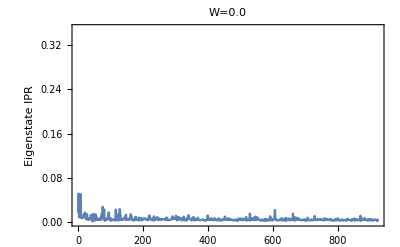

```mathematica
Show[ListLinePlot[findIPR[V],PlotRange->{All,{0,0.35}}],Frame->True,LabelStyle->Directive[Bold, Black,10],FrameLabel->{"",Style["Eigenstate IPR",Black,Bold,14]},PlotLabel->Style["W=0.0"]]
```

```mathematica
Export["/Users/aneekphys/Documents/MBL1 plots/EIPR_W0_L12.pdf",%]
```

/Users/aneekphys/Documents/MBL1 plots/EIPR_W0_L12.pdf

## Spectral Form Factor for L=10

```mathematica
SFF[Edata_,t_]:=(
Ni= Length[Edata];
Zt = 1/Ni Total[Exp[-I t #]&/@ Edata];
Return[Abs[Zt]^2]
)
```

```mathematica
mySFF[W_]:=(
eL = Range[-3,4,7/6000];
tList = 10^#&/@eL//N;
SFFfull = {};

For[p=1,p<=5,p++,

Haml = Hamiltonian1[1,W,12][[1]]//SparseArray;
En = Eigenvalues[Haml];

SFFList = SFF[En,#]&/@tList;

AppendTo[SFFfull,SFFList]

];

Return[Total[SFFfull]/5]





)
```

Eigenvalues::arh: Because finding 924 out of the 924 eigenvalues and/or eigenvectors is likely to be faster with dense matrix methods, the sparse input matrix will be converted. If fewer eigenvalues and/or eigenvectors would be sufficient, consider restricting this number using the second argument to Eigenvalues.

General::stop: Further output of Eigenvalues::arh will be suppressed during this calculation.

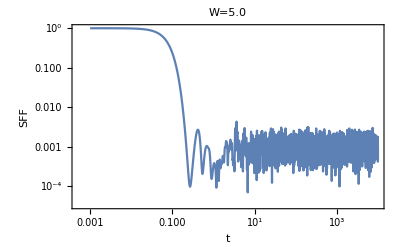

```mathematica
Show[ListLinePlot[Transpose[{tList,mySFF[5.0]}],ScalingFunctions->{"Log10","Log10"}],Frame->True,LabelStyle->Directive[Bold, Black,10],FrameLabel->{Style["t",Black,Bold,14],Style["SFF",Black,Bold,14]},PlotLabel->Style["W=5.0"]]
```

```mathematica
Export["/Users/aneekphys/Documents/MBL1 plots/SFF_W5_L12.pdf",%]
```

/Users/aneekphys/Documents/MBL1 plots/SFF_W5_L12.pdf

## State Analysis

#### W = 0.075 (integrable region of disordered Heisenberg Spin model)

```mathematica
HamW0pt075 = Hamiltonian1[1,5.5,10][[1]];
```

```mathematica
{En,V} = Eigensystem[HamW0pt075];
eigenPairs=Transpose[{En,V}];
sortedEigenPairs=SortBy[eigenPairs,First];
En=sortedEigenPairs[[All,1]];
V=sortedEigenPairs[[All,2]];
```

```mathematica
GroundVec =V[[#]]&/@ Position[En,Min[En]]//Flatten//Normalize;
FloorVec =V[[#]]&/@ Position[En,Max[En]]//Flatten//Normalize;
TFDbeta0Vec = Total[Table[(Exp[-3.0(En[[k]]-En[[1]])]//N//Chop)V[[k]]//Normalize,{k,1,Length[V]}]]//Normalize;
randVecEigen = Total[Table[(RandomReal[])V[[k]]//Normalize,{k,1,Length[V]}]]//Normalize;
randVecPos = Table[RandomReal[],{k,1,Length[GroundVec]}]//Normalize;
FirstExVec = V[[-4]]//Normalize;
```

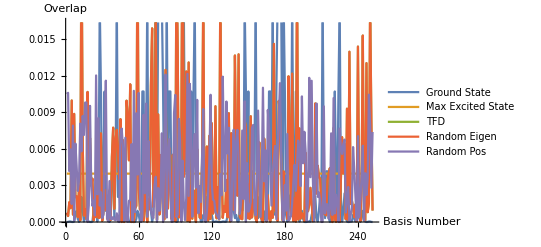

```mathematica
ListLinePlot[{Abs[#]^2&/@GroundVec,Abs[#]^2&/@FloorVec,Abs[#]^2&/@TFDbeta0Vec,Abs[#]^2&/@randVecEigen,Abs[#]^2&/@randVecPos},AxesLabel->{"Basis Number","Overlap"},PlotLegends->{"Ground State","Max Excited State","TFD","Random Eigen","Random Pos"}]
```

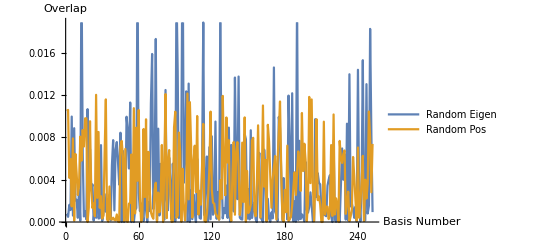

```mathematica
ListLinePlot[{Abs[#]^2&/@randVecEigen,Abs[#]^2&/@randVecPos},AxesLabel->{"Basis Number","Overlap"},PlotLegends->{"Random Eigen","Random Pos"}]
```

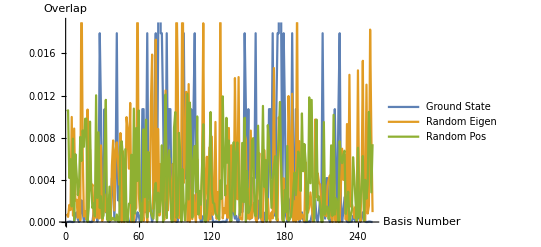

```mathematica
ListLinePlot[{Abs[#]^2&/@GroundVec,Abs[#]^2&/@randVecEigen,Abs[#]^2&/@randVecPos},AxesLabel->{"Basis Number","Overlap"},PlotLegends->{"Ground State","Random Eigen","Random Pos"}]
```

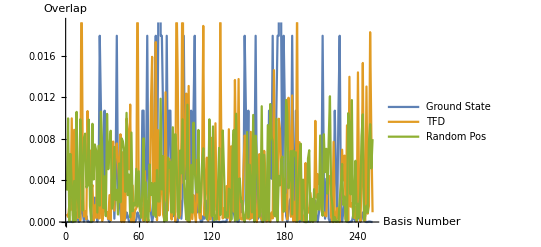

```mathematica
ListLinePlot[{Abs[#]^2&/@GroundVec,Abs[#]^2&/@TFDbeta0Vec,Abs[#]^2&/@randVecPos},AxesLabel->{"Basis Number","Overlap"},PlotLegends->{"Ground State","TFD","Random Pos"}]
```

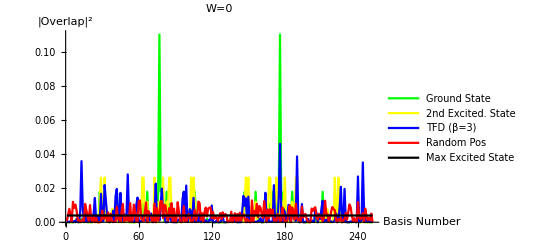

```mathematica
Show[ListLinePlot[{Abs[#]^2&/@GroundVec,Abs[#]^2&/@FirstExVec,Abs[#]^2&/@TFDbeta0Vec,Abs[#]^2&/@randVecPos,Abs[#]^2&/@FloorVec},AxesLabel->{"Basis Number","|Overlap|^2"},PlotLegends->{"Ground State","2nd Excited. State","TFD (β=3)","Random Pos","Max Excited State"},PlotStyle->{Green,Yellow,Blue,Red,Black},PlotRange->All],LabelStyle->Directive[Bold, Black],PlotLabel->"W=0"]
```

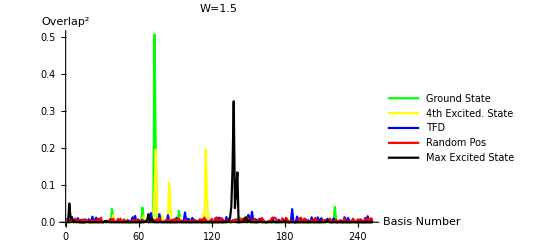

```mathematica
Show[ListLinePlot[{Abs[#]^2&/@GroundVec,Abs[#]^2&/@FirstExVec,Abs[#]^2&/@TFDbeta0Vec,Abs[#]^2&/@randVecPos,Abs[#]^2&/@FloorVec},AxesLabel->{"Basis Number","Overlap^2"},PlotLegends->{"Ground State","4th Excited. State","TFD","Random Pos","Max Excited State"},PlotStyle->{Green,Yellow,Blue,Red,Black},PlotRange->All],LabelStyle->Directive[Bold, Black],PlotLabel->"W=1.5"]
```

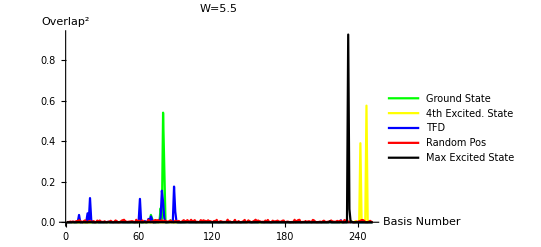

```mathematica
Show[ListLinePlot[{Abs[#]^2&/@GroundVec,Abs[#]^2&/@FirstExVec,Abs[#]^2&/@TFDbeta0Vec,Abs[#]^2&/@randVecPos,Abs[#]^2&/@FloorVec},AxesLabel->{"Basis Number","Overlap^2"},PlotLegends->{"Ground State","4th Excited. State","TFD","Random Pos","Max Excited State"},PlotStyle->{Green,Yellow,Blue,Red,Black},PlotRange->All],LabelStyle->Directive[Bold, Black],PlotLabel->"W=5.5"]
```

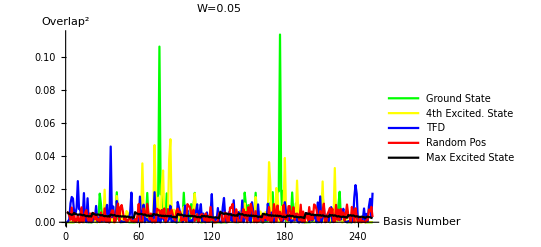

```mathematica
Show[ListLinePlot[{Abs[#]^2&/@GroundVec,Abs[#]^2&/@FirstExVec,Abs[#]^2&/@TFDbeta0Vec,Abs[#]^2&/@randVecPos,Abs[#]^2&/@FloorVec},AxesLabel->{"Basis Number","Overlap^2"},PlotLegends->{"Ground State","4th Excited. State","TFD","Random Pos","Max Excited State"},PlotStyle->{Green,Yellow,Blue,Red,Black},PlotRange->All],LabelStyle->Directive[Bold, Black],PlotLabel->"W=0.05"]
```

## Spread Complexity: Dissipative Dynamics in no-jump limit

What kind of dissipative jump operators can we consider ?

(1) Particle Loss/Gain type from the even sites. Consider non-Hermitian part of the Hamiltonian, , for  ∈ Evens.

(2) (A==-iα(σ_0^x σ_1^x+σ_0^y σ_1^y))^2

, here  is the non-Hermitian part

#### Define the non-Hermitian Hamiltonian

```mathematica
NonHHam[a_,g_,L_]:=(
op1 = KroneckerProduct[X,X,IdentityMatrix[2^(L-2)]]+ KroneckerProduct[Y,Y,IdentityMatrix[2^(L-2)]];
op2 = KroneckerProduct[IdentityMatrix[2^(L-2)],X,X]+ KroneckerProduct[IdentityMatrix[2^(L-2)],Y,Y];
A = - I a op1.op1 - I a op2.op2;
Mag = Total[Table[KroneckerProduct[IdentityMatrix[2^l,SparseArray],Z,IdentityMatrix[2^(L-l-1),SparseArray]],{l,0,L-1}]];
Pos = Position[Diagonal[Mag//Normal],0]//Flatten;
dim = Length[Pos];
ProjM = Vec[#,2^L]&/@Pos;
(ProjM.A.Transpose[ProjM])//Normal


);
```

```mathematica
Ham = Hamiltonian1[1,7.5,10][[1]]+NonHHam[0,0,10];
{En0,V0} =Eigensystem[ Hamiltonian1[1,0,10][[1]]];
{En,V} = Eigensystem[Ham];
vec = ConstantArray[0,En//Length];
vec = Total[Table[V[[k]]//Normalize,{k,1,En//Length}]];
(*vec =ConstantArray[0,En//Length];
vec[[10]]=1;*)
vec = Total[Table[V0[[k]]//Normalize,{k,1,En//Length}]];

vec = (vec//Normalize);
```

#### The bi-Lanczos Algorithm

```mathematica
randU = RandomVariate[CircularUnitaryMatrixDistribution[Length[vec]]];
wList = {0.01};
(*alList = {0.0,0.0005,0.001,0.005,0.01}*)
```

```mathematica
For[ind=1,ind<=Length[wList],ind++,
w= wList[[ind]];
compAv = {};
IPRAv = {};
EntAv = {};
For[p=0,p<100,p++,
H0 = Hamiltonian1[1,w,10][[1]];
Ham = H0+NonHHam[0,0,10];
{En0,V0} =Eigensystem[ H0+NonHHam[0,0,10]];
{En,V} = Eigensystem[Ham];
(*vec = ConstantArray[0,En//Length];
vec = Total[Table[V0[[k]]//Normalize,{k,1,En//Length}]];*)
vec =ConstantArray[0,En//Length];
vec[[77]]=1;
(*vec[[176]]=1;*)
(*vec = Total[Table[V0[[k]]//Normalize,{k,1,En//Length}]];*)
(*vec = V0[[2]];*)
randU = RandomVariate[CircularUnitaryMatrixDistribution[Length[vec]]];(* Haar random state*)
vec = randU.vec;

(*(*Generate a 292-dimensional random real matrix*)randomRealMatrix=RandomVariate[NormalDistribution[],{Length[En],Length[En]}];

 (*Perform QR decomposition and use the orthogonal part*)
    {q,r}=QRDecomposition[randomRealMatrix];

   (*Adjust the sign of columns to ensure Haar measure*)
     diagonal=Diagonal[r];
     signDiagonal=Sign[diagonal];
     haarRandomOrthogonalMatrix=q.DiagonalMatrix[signDiagonal];

vec = haarRandomOrthogonalMatrix.vec;*)

vec = (vec//Normalize);

gamma = 0;
alpha = 0;
psi0 = vec;
HamN =Ham ;
HamNd = ConjugateTranspose[Ham];
PnList = {psi0};
QnList = {psi0};
anList = {ConjugateTranspose[psi0].HamN.psi0};
bnList = {};
cnList = {};
(* constructing the bi-orthogonal Krylov basis*)
For[n=1,n<= Length[En],n++,
An = HamN.PnList[[-1]]-anList[[-1]] PnList[[-1]];
proj = ConstantArray[0,En//Length];
For[m=0,m<n,m++,
proj =proj+( ConjugateTranspose[QnList[[m+1]]].An) PnList[[m+1]];
];
An = An-proj;
proj = ConstantArray[0,En//Length];
For[m=0,m<n,m++,
proj =proj+( ConjugateTranspose[QnList[[m+1]]].An) PnList[[m+1]];
];
An = An-proj;

Bn = HamNd.QnList[[-1]]-Conjugate[anList[[-1]]] QnList[[-1]];
proj = ConstantArray[0,En//Length];
For[m=0,m<n,m++,
proj =proj+( ConjugateTranspose[PnList[[m+1]]].Bn) QnList[[m+1]];
];
Bn = Bn-proj;
proj = ConstantArray[0,En//Length];
For[m=0,m<n,m++,
proj =proj+( ConjugateTranspose[PnList[[m+1]]].Bn) QnList[[m+1]];
];
Bn = Bn-proj;
wn = ConjugateTranspose[An].Bn;
cn = Sqrt[Abs[wn]];
bn = Conjugate[wn]/cn;
Pn = An/cn;
Qn = Bn/Conjugate[bn];
an =  ConjugateTranspose[Qn].HamN.Pn;
If[cn<10^-10,
Break[],
AppendTo[PnList,Pn];
AppendTo[QnList,Qn];
AppendTo[bnList,bn];
AppendTo[cnList,cn];
AppendTo[anList,an]
];


];
dim = Length[En];
tList = Range[0dim,1.5dim,dim/100];

(*(* Logarithmic t-List*)

exp = Table[ex,{ex,2,3.5,1.5/75}];
tList = dim(10^#&/@exp)//N;
*)
complexityList = {};
iprList = {};
entList = {};
For[i=1,i<=Length[tList],i++,
t = tList[[i]];
psit = MatrixExp[-I HamN t ].psi0;
psit = psit//Normalize;

norm = 0;
comp=0;
ipr = 0;
ent = 0 ;
For[n=0,n<Length[PnList],n++,
Pn = PnList[[n+1]];
Qn = QnList[[n+1]];
phinq = ConjugateTranspose[Qn].psit;
phinp = ConjugateTranspose[Pn].psit;
pn = Abs[Conjugate[phinq] phinp];
norm = norm + Abs[Conjugate[phinq] phinp];
comp = comp+ n  Abs[Conjugate[phinq] phinp];
(*Print[phinq]*)
];
comp = comp/norm;
AppendTo[complexityList,comp];
ipr = 0;
ent = 0 ;
For[n=0,n<Length[PnList],n++,
Pn = PnList[[n+1]];
Qn = QnList[[n+1]];
phinq = ConjugateTranspose[Qn].psit;
phinp = ConjugateTranspose[Pn].psit;
pn = Abs[Conjugate[phinq] phinp]/norm;
ipr = ipr + pn^2;
ent = ent - pn Log[pn];
(*Print[phinq]*)
];
AppendTo[iprList,ipr];
AppendTo[entList,ent];
];
AppendTo[compAv,complexityList];
AppendTo[IPRAv,iprList];
AppendTo[EntAv,entList];
(*Print[p]*)

];
compAv = (1/100 Total[compAv]);
IPRAv = 1/100 Total[IPRAv];
EntAv = 1/100 Total[EntAv];
SetDirectory["/Users/aneekphys/Library/CloudStorage/OneDrive-IndianInstituteofScience/Projects/MBL_SYK_project/MBL_Data/Delta1_alpha_0_unitary_Haar/L10"];
Export["complexity_L_10_alpha_0.0000_w_"<>ToString[w]<>"_R_100.txt",compAv/dim,"Table"];
Export["KIPR_L_10_alpha_0.0000_w_"<>ToString[w]<>"_R_100.txt",IPRAv,"Table"];
Export["krylov_entropy_L_10_alpha_0.0000_w_"<>ToString[w]<>"_R_100.txt",EntAv,"Table"];
Export["an_L_10_alpha_0.0000_w_"<>ToString[w]<>"_R_100.txt",anList,"Table"];
Export["cn_L_10_alpha_0.0000_w_"<>ToString[w]<>"_R_100.txt",cnList,"Table"];
Export["tList_L_10_alpha_0.0000_w_"<>ToString[w]<>"_R_100.txt",tList/dim,"Table"];

(*Export["complexity_L_10_alpha_"<>ToString[al]<>"_w_6.5_R_250.txt",compAv/dim,"Table"];
Export["KIPR_L_10_alpha_"<>ToString[al]<>"_w_6.5_R_250.txt",IPRAv,"Table"];
Export["krylov_entropy_L_10_alpha_"<>ToString[al]<>"_w_6.5_R_250.txt",EntAv,"Table"];
Export["an_L_10_alpha_"<>ToString[al]<>"_w_6.5_R_250.txt",anList,"Table"];
Export["cn_L_10_alpha_"<>ToString[al]<>"_w_6.5_R_250.txt",cnList,"Table"];
Export["tList_L_10_alpha_"<>ToString[al]<>"_w_6.5_R_250.txt",tList/dim,"Table"];*)

];
```

SetDirectory::cdir: Cannot set current directory to /Users/aneekphys/Library/CloudStorage/OneDrive-IndianInstituteofScience/Projects/MBL_SYK_project/MBL_Data/Delta1_unitary_Haar/L10.

#### The Arnoldi Algorithm

#### Haar Random State

```mathematica
(*Generate a 292-dimensional random complex matrix*)randomComplexMatrix=RandomComplex[NormalDistribution[0,1],{292,292}];

(*Perform QR decomposition and use the unitary part*)
{q,r}=QRDecomposition[randomComplexMatrix];
unitaryMatrix=q;

(*Verify that the matrix is unitary*)
isUnitary=(ConjugateTranspose[unitaryMatrix].unitaryMatrix//Chop)==IdentityMatrix[292]
```

True

```mathematica
(*Generate a 292-dimensional random unitary matrix using built-in capabilities*)unitaryMatrix=RandomVariate[CircularUnitaryMatrixDistribution[292]];

(*Verify that the matrix is unitary*)
isUnitary=(ConjugateTranspose[unitaryMatrix].unitaryMatrix//Chop)==IdentityMatrix[292]
```

True

## PLOTTING OPEN SYSTEM....

#### NEEL

```mathematica
KCNeelOpenW6pt5 = Import["/Users/aneekphys/Library/CloudStorage/OneDrive-IndianInstituteofScience/Projects/MBL_SYK_project/MBL_Data/Delta1_alpha_0.0001_Neel/L10/complexity_L_10_alpha_0.0001_w_6.5_R_75.txt","Table"]//Flatten;
KCNeelOpenW1pt0 = Import["/Users/aneekphys/Library/CloudStorage/OneDrive-IndianInstituteofScience/Projects/MBL_SYK_project/MBL_Data/Delta1_alpha_0.0001_Neel/L10/complexity_L_10_alpha_0.0001_w_1.0_R_75.txt","Table"]//Flatten;
KCNeelOpenW0pt1 = Import["/Users/aneekphys/Library/CloudStorage/OneDrive-IndianInstituteofScience/Projects/MBL_SYK_project/MBL_Data/Delta1_alpha_0.0001_Neel/L10/complexity_L_10_alpha_0.0001_w_0.1_R_75.txt","Table"]//Flatten;
KCNeelOpenW0pt01 = Import["/Users/aneekphys/Library/CloudStorage/OneDrive-IndianInstituteofScience/Projects/MBL_SYK_project/MBL_Data/Delta1_alpha_0.0001_Neel/L10/complexity_L_10_alpha_0.0001_w_0.01_R_75.txt","Table"]//Flatten;
tList = Import["/Users/aneekphys/Library/CloudStorage/OneDrive-IndianInstituteofScience/Projects/MBL_SYK_project/MBL_Data/Delta1_alpha_0.0001_TFD/L10/tList_L_10_alpha_0.0001_w_0.1_R_75.txt","Table"]//Flatten;
```

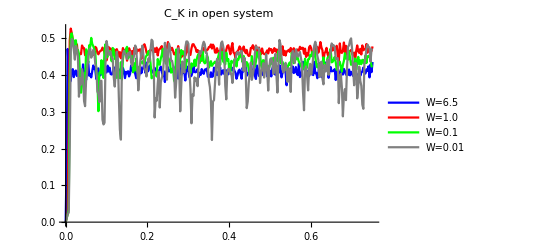

```mathematica
ListLinePlot[{Transpose[{tList,KCNeelOpenW6pt5}],Transpose[{tList,KCNeelOpenW1pt0}],Transpose[{tList,KCNeelOpenW0pt1}],Transpose[{tList,KCNeelOpenW0pt01}]},PlotStyle->{Blue,Red,Green,Gray},PlotLegends->{"W=6.5","W=1.0","W=0.1","W=0.01"},PlotLabel->"C_K in open system",LabelStyle->Directive[Bold, Black]]
```

```mathematica
KIPRNeelOpenW6pt5 = Import["/Users/aneekphys/Library/CloudStorage/OneDrive-IndianInstituteofScience/Projects/MBL_SYK_project/MBL_Data/Delta1_alpha_0.0001_Neel/L10/KIPR_L_10_alpha_0.0001_w_6.5_R_75.txt","Table"]//Flatten;
KIPRNeelOpenW1pt0 = Import["/Users/aneekphys/Library/CloudStorage/OneDrive-IndianInstituteofScience/Projects/MBL_SYK_project/MBL_Data/Delta1_alpha_0.0001_Neel/L10/KIPR_L_10_alpha_0.0001_w_1.0_R_75.txt","Table"]//Flatten;
KIPRNeelOpenW0pt1 = Import["/Users/aneekphys/Library/CloudStorage/OneDrive-IndianInstituteofScience/Projects/MBL_SYK_project/MBL_Data/Delta1_alpha_0.0001_Neel/L10/KIPR_L_10_alpha_0.0001_w_0.1_R_75.txt","Table"]//Flatten;
KIPRNeelOpenW0pt01 = Import["/Users/aneekphys/Library/CloudStorage/OneDrive-IndianInstituteofScience/Projects/MBL_SYK_project/MBL_Data/Delta1_alpha_0.0001_Neel/L10/KIPR_L_10_alpha_0.0001_w_0.01_R_75.txt","Table"]//Flatten;
tList = Import["/Users/aneekphys/Library/CloudStorage/OneDrive-IndianInstituteofScience/Projects/MBL_SYK_project/MBL_Data/Delta1_alpha_0.0001_TFD/L10/tList_L_10_alpha_0.0001_w_0.1_R_75.txt","Table"]//Flatten;
```

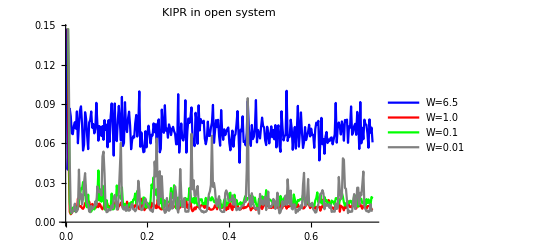

```mathematica
ListLinePlot[{Transpose[{tList,KIPRNeelOpenW6pt5}],Transpose[{tList,KIPRNeelOpenW1pt0}],Transpose[{tList,KIPRNeelOpenW0pt1}],Transpose[{tList,KIPRNeelOpenW0pt01}]},PlotStyle->{Blue,Red,Green,Gray},PlotLegends->{"W=6.5","W=1.0","W=0.1","W=0.01"},PlotLabel->"KIPR in open system",LabelStyle->Directive[Bold, Black]]
```

#### TFD

```mathematica
KCTFDOpenW6pt5 = Import["/Users/aneekphys/Library/CloudStorage/OneDrive-IndianInstituteofScience/Projects/MBL_SYK_project/MBL_Data/Delta1_alpha_0.0001_TFD/L10/complexity_L_10_alpha_0.0001_w_6.5_R_75.txt","Table"]//Flatten;
KCTFDOpenW1pt0 = Import["/Users/aneekphys/Library/CloudStorage/OneDrive-IndianInstituteofScience/Projects/MBL_SYK_project/MBL_Data/Delta1_alpha_0.0001_TFD/L10/complexity_L_10_alpha_0.0001_w_1.0_R_75.txt","Table"]//Flatten;
KCTFDOpenW0pt1 = Import["/Users/aneekphys/Library/CloudStorage/OneDrive-IndianInstituteofScience/Projects/MBL_SYK_project/MBL_Data/Delta1_alpha_0.0001_TFD/L10/complexity_L_10_alpha_0.0001_w_0.1_R_75.txt","Table"]//Flatten;
tList = Import["/Users/aneekphys/Library/CloudStorage/OneDrive-IndianInstituteofScience/Projects/MBL_SYK_project/MBL_Data/Delta1_alpha_0.0001_TFD/L10/tList_L_10_alpha_0.0001_w_0.1_R_75.txt","Table"]//Flatten;
```

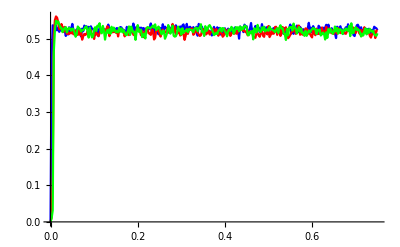

```mathematica
ListLinePlot[{Transpose[{tList,KCTFDOpenW6pt5}],Transpose[{tList,KCTFDOpenW1pt0}],Transpose[{tList,KCTFDOpenW0pt1}]},PlotStyle->{Blue,Red,Green},PlotRange->All]
```

```mathematica
KIPRTFDOpenW6pt5 = Import["/Users/aneekphys/Library/CloudStorage/OneDrive-IndianInstituteofScience/Projects/MBL_SYK_project/MBL_Data/Delta1_alpha_0.0001_TFD/L10/KIPR_L_10_alpha_0.0001_w_6.5_R_75.txt","Table"]//Flatten;
KIPRTFDOpenW1pt0 = Import["/Users/aneekphys/Library/CloudStorage/OneDrive-IndianInstituteofScience/Projects/MBL_SYK_project/MBL_Data/Delta1_alpha_0.0001_TFD/L10/KIPR_L_10_alpha_0.0001_w_1.0_R_75.txt","Table"]//Flatten;
KIPRTFDOpenW0pt1 = Import["/Users/aneekphys/Library/CloudStorage/OneDrive-IndianInstituteofScience/Projects/MBL_SYK_project/MBL_Data/Delta1_alpha_0.0001_TFD/L10/KIPR_L_10_alpha_0.0001_w_0.1_R_75.txt","Table"]//Flatten;
tList = Import["/Users/aneekphys/Library/CloudStorage/OneDrive-IndianInstituteofScience/Projects/MBL_SYK_project/MBL_Data/Delta1_alpha_0.0001_TFD/L10/tList_L_10_alpha_0.0001_w_0.1_R_75.txt","Table"]//Flatten;
```

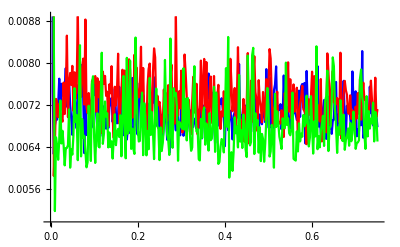

```mathematica
ListLinePlot[{Transpose[{tList,KIPRTFDOpenW6pt5}],Transpose[{tList,KIPRTFDOpenW1pt0}],Transpose[{tList,KIPRTFDOpenW0pt1}]},PlotStyle->{Blue,Red,Green},PlotRange->Automatic]
```

## PLOTTING CLOSED SYSTEM

#### NEEL

```mathematica
KCNeelClosedW6pt5 = Import["/Users/aneekphys/Library/CloudStorage/OneDrive-IndianInstituteofScience/Projects/MBL_SYK_project/MBL_Data/Delta1_alpha_0_Neel/L10/complexity_L_10_alpha_0.0000_w_6.5_R_75.txt","Table"]//Flatten;
KCNeelClosedW1pt0 = Import["/Users/aneekphys/Library/CloudStorage/OneDrive-IndianInstituteofScience/Projects/MBL_SYK_project/MBL_Data/Delta1_alpha_0_Neel/L10/complexity_L_10_alpha_0.0000_w_1.0_R_75.txt","Table"]//Flatten;
KCNeelClosedW0pt1 = Import["/Users/aneekphys/Library/CloudStorage/OneDrive-IndianInstituteofScience/Projects/MBL_SYK_project/MBL_Data/Delta1_alpha_0_Neel/L10/complexity_L_10_alpha_0.0000_w_0.1_R_75.txt","Table"]//Flatten;
KCNeelClosedW0pt01 = Import["/Users/aneekphys/Library/CloudStorage/OneDrive-IndianInstituteofScience/Projects/MBL_SYK_project/MBL_Data/Delta1_alpha_0_Neel/L10/complexity_L_10_alpha_0.0000_w_0.01_R_75.txt","Table"]//Flatten;
tList = Import["/Users/aneekphys/Library/CloudStorage/OneDrive-IndianInstituteofScience/Projects/MBL_SYK_project/MBL_Data/Delta1_alpha_0.0001_TFD/L10/tList_L_10_alpha_0.0001_w_0.1_R_75.txt","Table"]//Flatten;
```

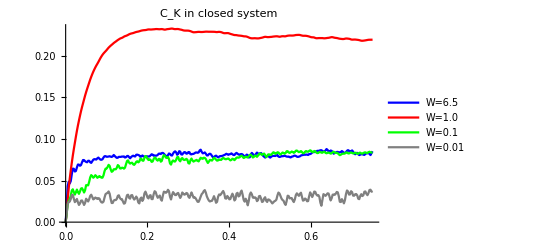

```mathematica
ListLinePlot[{Transpose[{tList,KCNeelClosedW6pt5}],Transpose[{tList,KCNeelClosedW1pt0}],Transpose[{tList,KCNeelClosedW0pt1}],Transpose[{tList,KCNeelClosedW0pt01}]},PlotStyle->{Blue,Red,Green,Gray},PlotLegends->{"W=6.5","W=1.0","W=0.1","W=0.01"},PlotLabel->"C_K in closed system",LabelStyle->Directive[Bold, Black]]
```

```mathematica
KIPRNeelClosedW6pt5 = Import["/Users/aneekphys/Library/CloudStorage/OneDrive-IndianInstituteofScience/Projects/MBL_SYK_project/MBL_Data/Delta1_alpha_0_Neel/L10/KIPR_L_10_alpha_0.0000_w_6.5_R_75.txt","Table"]//Flatten;
KIPRNeelClosedW1pt0 = Import["/Users/aneekphys/Library/CloudStorage/OneDrive-IndianInstituteofScience/Projects/MBL_SYK_project/MBL_Data/Delta1_alpha_0_Neel/L10/KIPR_L_10_alpha_0.0000_w_1.0_R_75.txt","Table"]//Flatten;
KIPRNeelClosedW0pt1 = Import["/Users/aneekphys/Library/CloudStorage/OneDrive-IndianInstituteofScience/Projects/MBL_SYK_project/MBL_Data/Delta1_alpha_0_Neel/L10/KIPR_L_10_alpha_0.0000_w_0.1_R_75.txt","Table"]//Flatten;
KIPRNeelClosedW0pt01 = Import["/Users/aneekphys/Library/CloudStorage/OneDrive-IndianInstituteofScience/Projects/MBL_SYK_project/MBL_Data/Delta1_alpha_0_Neel/L10/KIPR_L_10_alpha_0.0000_w_0.01_R_75.txt","Table"]//Flatten;
tList = Import["/Users/aneekphys/Library/CloudStorage/OneDrive-IndianInstituteofScience/Projects/MBL_SYK_project/MBL_Data/Delta1_alpha_0.0001_TFD/L10/tList_L_10_alpha_0.0001_w_0.1_R_75.txt","Table"]//Flatten;
```

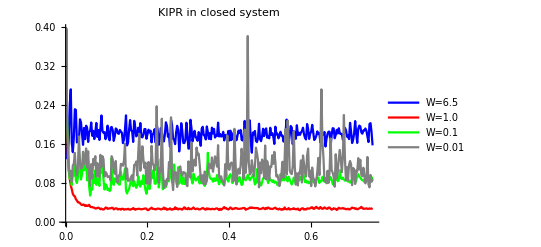

```mathematica
ListLinePlot[{Transpose[{tList,KIPRNeelClosedW6pt5}],Transpose[{tList,KIPRNeelClosedW1pt0}],Transpose[{tList,KIPRNeelClosedW0pt1}],Transpose[{tList,KIPRNeelClosedW0pt01}]},PlotStyle->{Blue,Red,Green,Gray},PlotLegends->{"W=6.5","W=1.0","W=0.1","W=0.01"},PlotLabel->"KIPR in closed system",LabelStyle->Directive[Bold, Black]]
```

```mathematica
vec//Norm
```

1.

```mathematica
ConjugateTranspose[PnList[[78]]].QnList[[78]]//Chop
```

1.

```mathematica
anList
```

```mathematica
vec//Norm
```

1.

```mathematica
ConjugateTranspose[PnList[[5]]].QnList[[85]]//Chop
```

0

```mathematica
QnList[[90]]//Norm
```

1.

```mathematica
complexityList/252
```

{5.33744×10^-32,0.0532192,0.0949872,0.126841,0.152571,0.174649,0.191215,0.206263,0.219146,0.226034,0.232127,0.238339,0.245466,0.250745,0.258619,0.2653,0.27364,0.280386,0.284941,0.28925,0.291203,0.292065,0.295254,0.298257,0.299933,0.298362,0.298259,0.300707,0.303214,0.305717,0.309386,0.313392,0.314029,0.311383,0.311802,0.31697,0.319261,0.321983,0.322847,0.320448,0.320407,0.321095,0.322599,0.325621,0.325065,0.323233,0.327019,0.331735,0.337782,0.340967,0.341042,0.337604,0.332852,0.328202,0.323367,0.322252,0.327306,0.327156,0.325172,0.326028,0.326156,0.325328,0.325398,0.32686,0.327556,0.328803,0.328969,0.328633,0.328998,0.328842,0.324921,0.319414,0.312231,0.306592,0.308169,0.309428,0.310904,0.314835,0.317493,0.321419,0.323194,0.325727,0.326938,0.324461,0.322494,0.320228,0.313865,0.307153,0.301595,0.301179,0.302967,0.305624,0.307325,0.309479,0.311066,0.308213,0.309755,0.310833,0.314294,0.316878,0.317544,0.322619,0.320562,0.319963,0.323787,0.325806,0.32429,0.325164,0.32535,0.321632,0.319816,0.317329,0.315519,0.317609,0.321775,0.325022,0.327322,0.325903,0.32353,0.322813,0.323314,0.325483,0.326178,0.326782,0.326836,0.323923,0.321093,0.323459,0.325774,0.327352,0.326997,0.327283,0.328772,0.329015,0.328968,0.326085,0.325511,0.328767,0.33453,0.338706,0.340095,0.337222,0.334346,0.333523,0.334873,0.33573,0.337867,0.340867,0.341199,0.339288,0.334475}